# 6. GRAFOS REGULARES Y COMPLETOS. SUBGRAFOS Y GRAFOS BIPARTITOS

*Las entradas de cada ejemplo deben ser ejecutados en orden para su correcto funcionamiento.

1. GRADO DE UN VÉRTICE

### 1.1. EL GRADO EN GRAFOS NO DIRIGIDOS

#### Función 6.1. GRADO[]

```mathematica
GRADO[n_,F_]:=Module[{i},
grado=0;
Do[If[Intersection[{F[[i]][[1]],F[[i]][[2]]},{n}]=={n},grado++],{i,Length[F]}];
grado
]
```

#### Función 6.2. GRADO2[]

```mathematica
GRADO2[n_,matrizadyacencia_]:=
   MatrixPower[matrizadyacencia,2][[n,n]];
```

#### Función 6.3. GRADO3[]

```mathematica
GRADO3[n_,matrizincidencia_]:=Sum[
   matrizincidencia[[n,i]]
,{i,Dimensions[matrizincidencia][[2]]}];
```

#### Ejemplo 6.1.

```mathematica
W={1,2,3,4,5};
F={1->2,1->3,2->3,1->4,2->4,3->4,1->5,2->5,3->5,4->5};
```

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{k,i,j},
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[F[[k,1]],F[[k,2]]]]=1;
matrizadyacencia[[F[[k,2]],F[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
```

```mathematica
MATRIZINCIDENCIA[W_,F_]:=Module[{i,j},
matrizincidencia=Table[0,{i,Length[W]},{j,Length[F]}];
Do[Do[
matrizincidencia[[F[[j]][[i]],j]]=1;
,{i,2}];,{j,Length[F]}];
matrizincidencia
];
```

```mathematica
GRADO[n_,F_]:=Module[{i},
grado=0;
Do[If[Intersection[{F[[i]][[1]],F[[i]][[2]]},{n}]=={n},grado++],{i,Length[F]}];
grado
]
```

```mathematica
Sum[GRADO[i,F],{i,Length[W]}]==Length[F]*2
```

True

```mathematica
A=MATRIZADYACENCIA[W,F]
```

{{0,1,1,1,1},{1,0,1,1,1},{1,1,0,1,1},{1,1,1,0,1},{1,1,1,1,0}}

```mathematica
GRADO2[n_,matrizadyacencia_]:=MatrixPower[matrizadyacencia,2][[n,n]];
```

```mathematica
Sum[GRADO2[i,MATRIZADYACENCIA[W,F]],{i,Length[W]}]==Length[F]*2
```

True

```mathematica
GRADO3[n_,matrizincidencia_]:=Sum[matrizincidencia[[n,i]],{i,Dimensions[matrizincidencia][[2]]}];
```

```mathematica
Sum[GRADO3[i,MATRIZINCIDENCIA[W,F]],{i,Length[W]}]==Length[F]*2
```

True

```mathematica
<<Combinatorica`
```

```mathematica
grados=Degrees[FromAdjacencyMatrix[A]]
```

{4,4,4,4,4}

```mathematica
Sum[grados[[i]],{i,Length[grados]}]==Length[F]*2
```

True

### 1.2. EL GRADO EN GRAFOS DIRIGIDOS

#### Función 6.4. GRADOENTRADA[]

```mathematica
GRADOENTRADA[n_,F_]:=Module[{i},
grado=0;
Do[If[F[[i,2]]==n,grado++],{i,Length[F]}];
grado
]
```

#### Función 6.5. GRADOSALIDA[]

```mathematica
GRADOSALIDA[n_,F_]:=Module[{i},
grado=0;
Do[If[F[[i,1]]==n,grado++],{i,Length[F]}];
grado
]
```

#### Ejemplo 6.2.

a)

```mathematica
W={1,2,3,4,5};
F={1->2,2->3,3->4};
```

```mathematica
GRADO[n_,F_]:=Module[{i},
grado=0;
Do[If[Intersection[{F[[i]][[1]],F[[i]][[2]]},{n}]=={n},grado++],{i,Length[F]}];
grado
]
```

```mathematica
Do[If[GRADO[i,F]==0,Print["El vértice ",i," es aislado"]],{i,Length[W]}]
```

El vértice 5 es aislado

b)

```mathematica
matrizadyacencia={{0,1,1,1,0},{0,0,1,0,0},{0,0,0,0,0},{0,0,1,0,0},{0,1,1,1,0}};
```

```mathematica
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}]
F={};
Do[
Do[
If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];
,{i,Dimensions[matrizadyacencia][[1]]}];
,{j,Dimensions[matrizadyacencia][[1]]}];
F
```

{1,2,3,4,5}

{1→2,5→2,1→3,2→3,4→3,5→3,1→4,5→4}

```mathematica
GRADOENTRADA[n_,F_]:=Module[{i},
grado=0;
Do[If[F[[i,2]]==n,grado++],{i,Length[F]}];
grado
]
```

```mathematica
GRADOSALIDA[n_,F_]:=Module[{i},
grado=0;
Do[If[F[[i,1]]==n,grado++],{i,Length[F]}];
grado
]
```

```mathematica
Do[If[GRADOENTRADA[i,F]==0,Print["El vértice ",i," es una fuente"]],{i,Length[W]}]
Do[If[GRADOSALIDA[i,F]==0,Print["El vértice ",i," es un sumidero"]],{i,Length[W]}]
```

El vértice 1 es una fuente

El vértice 5 es una fuente

El vértice 3 es un sumidero

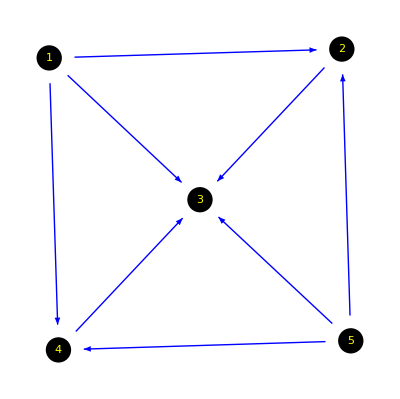

```mathematica
GRAFO=matrizadyacencia;
GraphPlot[GRAFO,VertexRenderingFunction->({Black,Disk[#,.05],Yellow,Text[#2,#1]}&),EdgeRenderingFunction->({Blue,Arrow[#1,0.1]}&),BaseStyle->{FontSize->14}]
```

```mathematica
<<Combinatorica`
```

```mathematica
InDegree[FromAdjacencyMatrix[matrizadyacencia,Type->Directed]]
```

{0,2,4,2,0}

```mathematica
OutDegree[FromAdjacencyMatrix[matrizadyacencia,Type->Directed]]
```

{3,1,0,1,3}

## 2. GRAFOS REGULARES Y COMPLETOS

### 2.1. Grafos regulares

#### Función 6.6. REGULAR[]

```mathematica
REGULAR[matrizadyacencia_]:=Module[{i,j},
grado=Sum[matrizadyacencia[[1,j]],{j,Dimensions[matrizadyacencia][[1]]}];
regular=True;
Do[
If[grado!=Sum[matrizadyacencia[[i,j]],{j,1,Dimensions[matrizadyacencia][[1]]}],regular=False;Break[];];
,{i,2,Dimensions[matrizadyacencia][[1]]}];
regular
];
```

#### Función 6.6.bis. REGULAR[]

```mathematica
REGULAR[matrizadyacencia_]:=Module[{i,j},
A=MatrixPower[matrizadyacencia,2];
grado=A[[1,1]];
regular=True;
Do[
If[grado!=A[[i,i]],regular=False;Break[];];
,{i,2,Dimensions[matrizadyacencia][[1]]}];
regular
];
```

#### Función 6.7. REGULAR2[]

```mathematica
REGULAR2[W_,F_]:=Module[{i,j},
grado=GRADO[W[[1]],F];
regular=True;
Do[
If[grado≠GRADO[W[[i]],F],regular=False];
,{i,2,Length[W]}];
If[regular,Print["El grafo es ",grado,"-regular"],Print["El grafo no es regular"];]
];
```

#### Ejemplo 6.3.

1

```mathematica
GRADO[n_,F_]:=Module[{i},
grado=0;
Do[If[Intersection[{F[[i]][[1]],F[[i]][[2]]},{n}]=={n},grado++],{i,Length[F]}];
grado
]
```

```mathematica
REGULAR2[W_,F_]:=Module[{i,j},
grado=GRADO[W[[1]],F];
regular=True;
Do[
If[grado≠GRADO[W[[i]],F],regular=False];
,{i,2,Length[W]}];
If[regular,Print["El grafo es ",grado,"-regular"],Print["El grafo no es regular"];]
];
```

```mathematica
W={1,2,3,4,5};
F={1->2,1->3,2->3,2->4,3->4,1->5,3->5,4->5};
REGULAR2[W,F]
```

El grafo no es regular

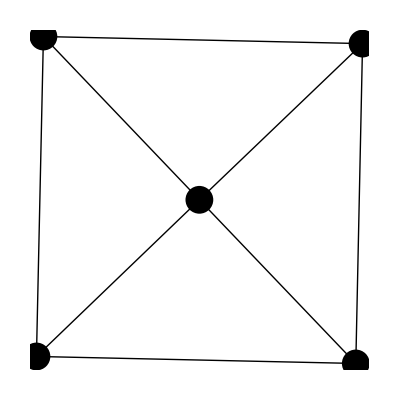

```mathematica
GraphPlot[F,PlotStyle->{Black,PointSize[.05]}]
```

2

```mathematica
REGULAR[matrizadyacencia_]:=Module[{i,j},
grado=Sum[matrizadyacencia[[1,j]],{j,Dimensions[matrizadyacencia][[1]]}];
regular=True;
Do[
If[grado!=Sum[matrizadyacencia[[i,j]],{j,1,Dimensions[matrizadyacencia][[1]]}],regular=False;Break[];];
,{i,2,Dimensions[matrizadyacencia][[1]]}];
regular
];
```

```mathematica
matrizadyacencia={{0,1,0,0,1},{1,0,1,0,0},{0,1,0,1,0},{0,0,1,0,1},{1,0,0,1,0}};
REGULAR[matrizadyacencia]
```

True

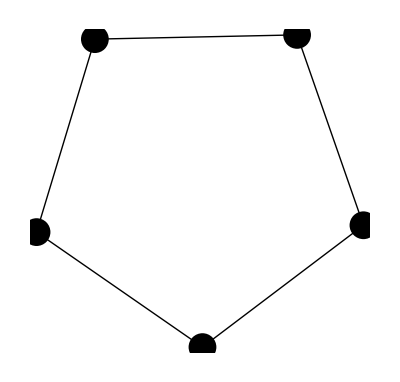

```mathematica
GraphPlot[matrizadyacencia,PlotStyle->{Black,PointSize[.05]}]
```

```mathematica
<<Combinatorica`
```

```mathematica
RegularQ[FromAdjacencyMatrix[matrizadyacencia]]
```

True

#### Ejemplo 6.4.

```mathematica
Añadirlado2[matrizadyacencia_]:=Module[{},
listamatrices={};
grados={};

A=matrizadyacencia.matrizadyacencia;
Do[
Do[
If[matrizadyacencia[[j,i]]==0,
matriz=matrizadyacencia;
matriz[[j,i]]=1;
matriz[[i,j]]=1;
AppendTo[listamatrices,matriz];
AppendTo[grados,{A[[i,i]],A[[j,j]]}];

];
,{j,i-1}];
,{i,Dimensions[matrizadyacencia][[1]]}];

posiciones=Table[{i},{i,Length[grados]}];
Isomorfas={};Isomorfas2={};
While[posiciones≠{},
parte=Union[Position[grados,grados[[posiciones[[1,1]]]]],Position[grados,{grados[[posiciones[[1,1]],2]],grados[[posiciones[[1,1]],1]]}]];
parte2=parte;

If[Length[parte2]>1,

Do[
A1=listamatrices[[parte2[[1,1]]]].listamatrices[[parte2[[1,1]]]];
A2=listamatrices[[parte2[[k1,1]]]].listamatrices[[parte2[[k1,1]]]];

A3=A1.listamatrices[[parte2[[1,1]]]];
A4=A2.listamatrices[[parte2[[k1,1]]]];
tabla3=Sort[Table[A3[[i1,i1]],{i1,n}]];
tabla4=Sort[Table[A4[[i1,i1]],{i1,n}]];

A5=A1.A1;
A6=A2.A2;
tabla5=Sort[Table[A5[[i1,i1]],{i1,n}]];
tabla6=Sort[Table[A6[[i1,i1]],{i1,n}]];


If[tabla3==tabla4 && tabla5==tabla6,
AppendTo[Isomorfas2,parte2[[k1]]];];

,{k1,2,Length[parte2]}];
parte2=Complement[parte2,Union[{parte[[1]]},Isomorfas2]];
Isomorfas=Union[Isomorfas,Isomorfas2];
Isomorfas2={};
];

posiciones=Complement[posiciones,parte];
];

listamatrices=Delete[listamatrices,Isomorfas]

];
```

```mathematica
QUITARISOMORFOS2[listamatrices_]:=Module[{i,i1,i2},
invariantes={};
posiblesisomorfos={};
Do[
A1=listamatrices[[i]].listamatrices[[i]];
tabla1=Sort[Table[A1[[i1,i1]],{i1,n}]];
A2=A1.listamatrices[[i]];
tabla2=Sort[Table[A2[[i1,i1]],{i1,n}]];
A3=A1.A1;
tabla3=Sort[Table[A3[[i1,i1]],{i1,n}]];

AppendTo[invariantes,{tabla1,tabla2,tabla3}];
,{i,Length[listamatrices]}];

posiciones=Table[{i},{i,Length[listamatrices]}];
While[posiciones≠{},
clase=Position[invariantes,invariantes[[posiciones[[1]][[1]]]]];
AppendTo[posiblesisomorfos,clase];
posiciones=Complement[posiciones,clase];
];
Print["DIVIDIMOS EN ",Length[posiblesisomorfos], " CLASES"];
listamat2={};
Do[
listamat=Table[listamatrices[[posiblesisomorfos[[j]][[k1]]]][[1]],{k1,Length[posiblesisomorfos[[j]]]}];
AppendTo[listamat2,listamat[[1]]];

,{j,Length[posiblesisomorfos]}];
listamat2
];
```

```mathematica
n=7;
nlados=14;
matrizadyacencia=Table[0,{i,n},{j,n}];
tiempo=TimeUsed[];
listamatrices1={matrizadyacencia};
listamatrices2=listamatrices1;
Do[

listamatrices3={};
Print["-------> Añadimos nuevo lado a ",Length[listamatrices2], " grafos"];
Do[
listamatrices3=Union[listamatrices3,Añadirlado2[listamatrices2[[k2]]]];
If[Mod[k2,100]==1,Print["Van ",k2];];
,{k2,Length[listamatrices2]}];
Print["************* DE ",k," LADOS: ",Length[listamatrices3]," *************"];

listamatrices2=QUITARISOMORFOS2[listamatrices3];

listamatrices1=Join[listamatrices1,listamatrices2];
Print[TimeUsed[]-tiempo,". Total: ",Length[listamatrices1]];

,{k,nlados}];
Print["Totales: ",Length[listamatrices1]," Tiempo empleado: ",TimeUsed[]-tiempo];
```

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 1 LADOS: 1 *************

DIVIDIMOS EN 1 CLASES

-5.68434×10^-14. Total: 2

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 2 LADOS: 2 *************

DIVIDIMOS EN 2 CLASES

0.015. Total: 4

-------> Añadimos nuevo lado a 2 grafos

Van 1

************* DE 3 LADOS: 7 *************

DIVIDIMOS EN 5 CLASES

0.015. Total: 9

-------> Añadimos nuevo lado a 5 grafos

Van 1

************* DE 4 LADOS: 20 *************

DIVIDIMOS EN 10 CLASES

0.031. Total: 19

-------> Añadimos nuevo lado a 10 grafos

Van 1

************* DE 5 LADOS: 57 *************

DIVIDIMOS EN 21 CLASES

0.078. Total: 40

-------> Añadimos nuevo lado a 21 grafos

Van 1

************* DE 6 LADOS: 148 *************

DIVIDIMOS EN 41 CLASES

0.172. Total: 81

-------> Añadimos nuevo lado a 41 grafos

Van 1

************* DE 7 LADOS: 304 *************

DIVIDIMOS EN 65 CLASES

0.343. Total: 146

-------> Añadimos nuevo lado a 65 grafos

Van 1

************* DE 8 LADOS: 498 *************

DIVIDIMOS EN 97 CLASES

0.64. Total: 243

-------> Añadimos nuevo lado a 97 grafos

Van 1

************* DE 9 LADOS: 715 *************

DIVIDIMOS EN 131 CLASES

1.109. Total: 374

-------> Añadimos nuevo lado a 131 grafos

Van 1

Van 101

************* DE 10 LADOS: 897 *************

DIVIDIMOS EN 148 CLASES

1.797. Total: 522

-------> Añadimos nuevo lado a 148 grafos

Van 1

Van 101

************* DE 11 LADOS: 948 *************

DIVIDIMOS EN 148 CLASES

2.593. Total: 670

-------> Añadimos nuevo lado a 148 grafos

Van 1

Van 101

************* DE 12 LADOS: 850 *************

DIVIDIMOS EN 131 CLASES

3.234. Total: 801

-------> Añadimos nuevo lado a 131 grafos

Van 1

Van 101

************* DE 13 LADOS: 655 *************

DIVIDIMOS EN 97 CLASES

3.64. Total: 898

-------> Añadimos nuevo lado a 97 grafos

Van 1

************* DE 14 LADOS: 437 *************

DIVIDIMOS EN 65 CLASES

3.89. Total: 963

Totales: 963 Tiempo empleado: 3.89

```mathematica
REGULAR[matrizadyacencia_]:=Module[{i,j},
grado=Sum[matrizadyacencia[[1,j]],{j,Dimensions[matrizadyacencia][[1]]}];
regular=True;
Do[
If[grado!=Sum[matrizadyacencia[[i,j]],{j,1,Dimensions[matrizadyacencia][[1]]}],regular=False;Break[];];
,{i,2,Dimensions[matrizadyacencia][[1]]}];
regular
];
```

```mathematica
<<"GraphUtilities`";
```

62

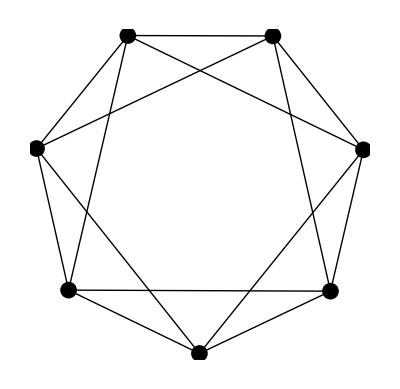

63

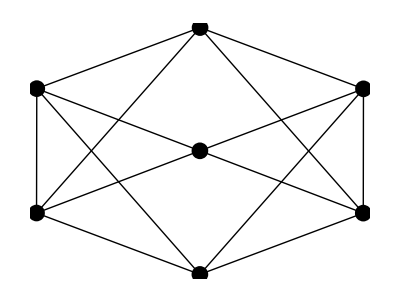

```mathematica
Do[
If[REGULAR[listamatrices2⟦i⟧],
Print[i];
Print[GraphPlot[listamatrices2⟦i⟧,PlotStyle->{Black,PointSize[.03]}]];
];
,{i,Length[listamatrices2]}]
```

### 2.2. Grafos completos

#### Función 6.8. COMPLETO[]

```mathematica
COMPLETO[matrizadyacencia_]:=   (Sum[MatrixPower[matrizadyacencia,2][[i,i]],{i,Dimensions[matrizadyacencia][[1]]}]==Dimensions[matrizadyacencia][[1]]*(Dimensions[matrizadyacencia][[1]]-1))
```

#### Ejemplo 6.5.

```mathematica
W1={1,2,3,4,5,6};
F1={1->2,2->3,3->4,4->5,5->6,6->1,2->4,2->5,4->6,2->6,3->6,3->5};
W2={1,2,3,4};
F2={1->2,2->3,3->4,4->1,2->4,3->1};
matrizadyacencia3={{0,1,1,1,1},{1,0,1,1,1},{1,1,0,1,1},{1,1,1,0,1},{1,1,1,1,0}};
matrizincidencia4={{1,0,0,0,0,1,0,0,0,1,0,0,1,0,1},{1,1,0,0,0,0,1,0,0,0,1,0,0,1,0},{0,1,1,0,0,1,0,1,0,0,0,1,0,0,0},{0,0,1,1,0,0,1,0,1,0,0,0,1,0,0},{0,0,0,1,1,0,0,1,0,1,0,0,0,1,0},{0,0,0,0,1,0,0,0,1,0,1,1,0,0,1}};
```

a) y b)

```mathematica
Length[F1]==Length[W1]*(Length[W1]-1)/2
```

False

```mathematica
Length[F2]==Length[W2]*(Length[W2]-1)/2
```

True

```mathematica
GRADO[n_,F_]:=Module[{i},
grado=0;
Do[If[Intersection[{F[[i]][[1]],F[[i]][[2]]},{n}]=={n},grado++],{i,Length[F]}];
grado
]
```

```mathematica
REGULAR2[W_,F_]:=Module[{i,j},
grado=GRADO[W[[1]],F];
regular=True;
Do[
If[grado≠GRADO[W[[i]],F],regular=False];
,{i,2,Length[W]}];
If[regular,Print["El grafo es ",grado,"-regular"],Print["El grafo no es regular"];]
];
```

```mathematica
REGULAR2[W1,F1]
```

El grafo no es regular

```mathematica
REGULAR2[W2,F2]
```

El grafo es 3-regular

```mathematica
grado==Length[W2]-1
```

True

c)

```mathematica
COMPLETO[matrizadyacencia_]:=   (Sum[MatrixPower[matrizadyacencia,2][[i,i]],{i,Dimensions[matrizadyacencia][[1]]}]==Dimensions[matrizadyacencia][[1]]*(Dimensions[matrizadyacencia][[1]]-1))
```

```mathematica
COMPLETO[matrizadyacencia3]
```

True

```mathematica
<<Combinatorica`
```

```mathematica
CompleteQ[FromAdjacencyMatrix[matrizadyacencia3]]
```

True

```mathematica
REGULAR[matrizadyacencia3]
```

True

d)

```mathematica
p=Dimensions[matrizincidencia4][[1]];
q=Dimensions[matrizincidencia4][[2]];
q==p*(p-1)/2
```

True

#### Ejemplo 6.6.

K_2

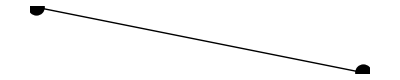

K_3

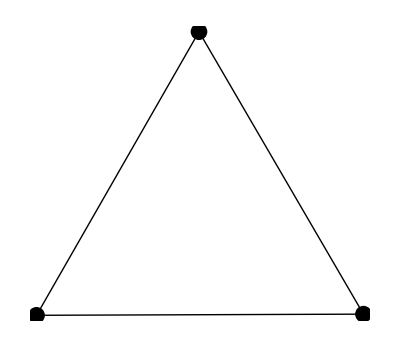

K_4

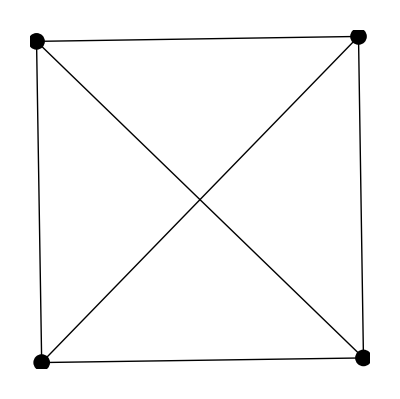

K_5

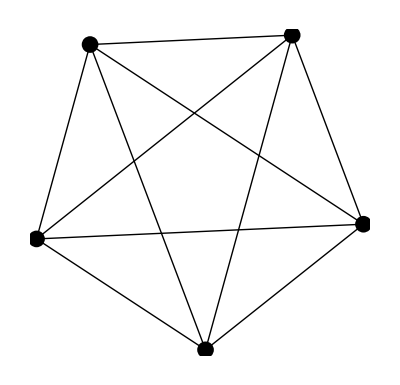

K_6

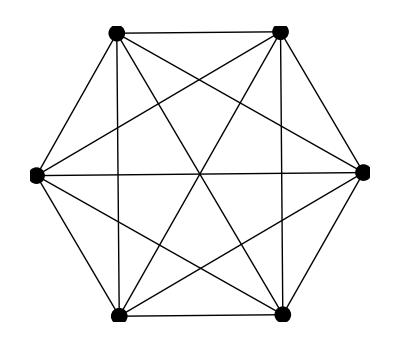

K_7

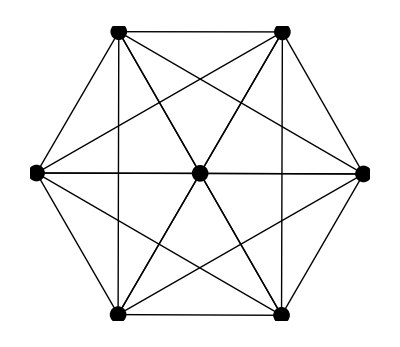

K_8

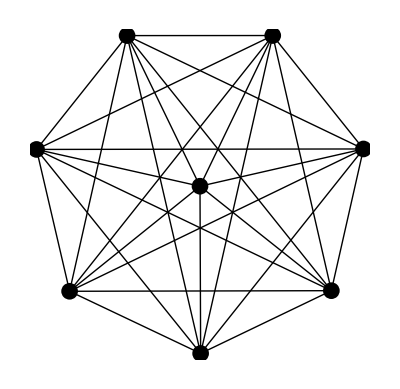

K_9

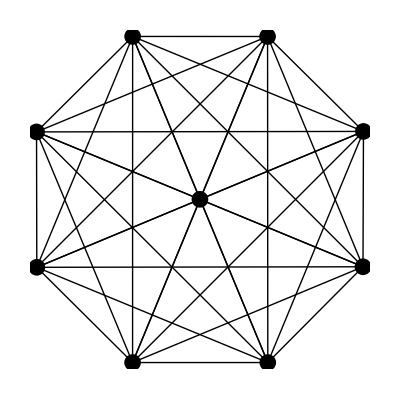

K_10

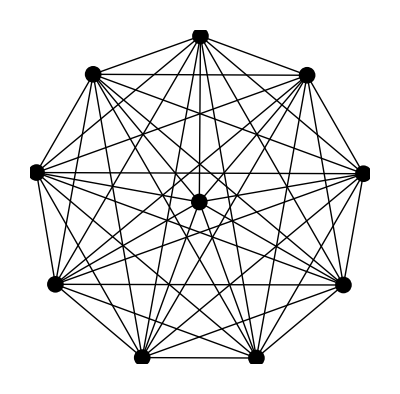

K_11

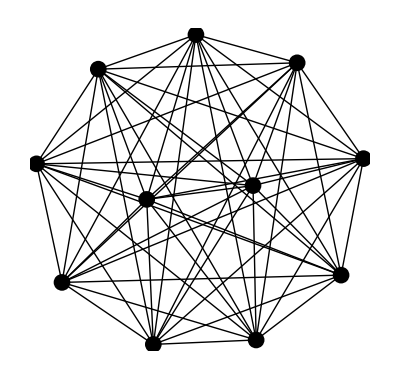

K_12

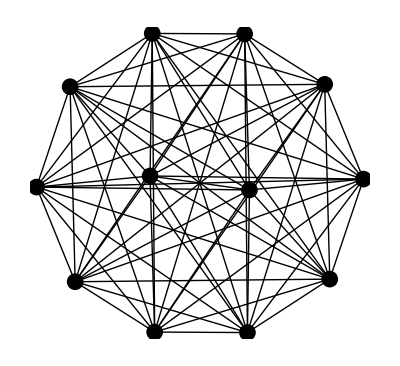

K_13

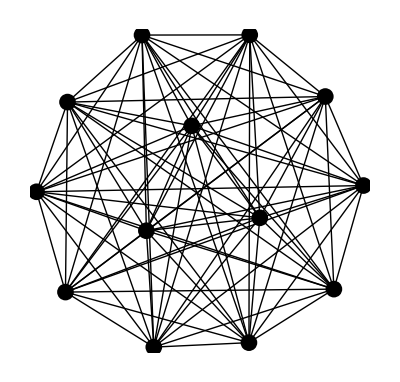

K_14

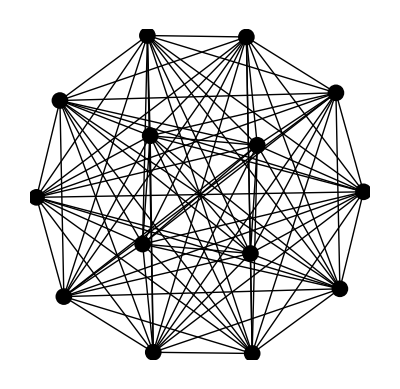

K_15

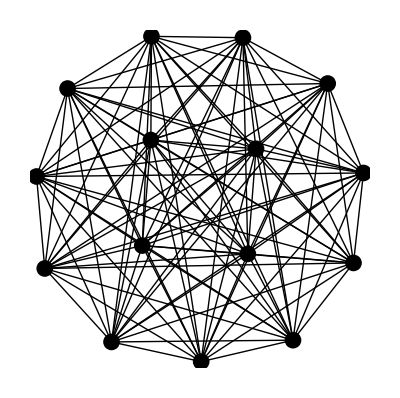

K_16

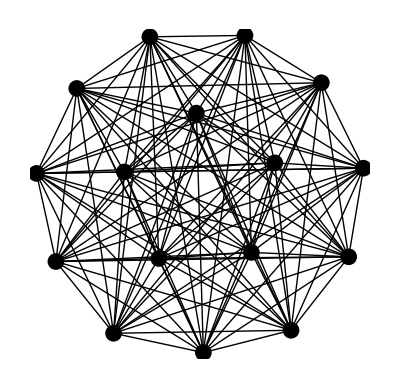

K_17

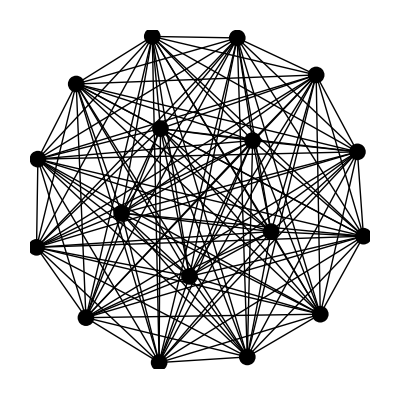

```mathematica
Do[
Print[Subscript["K", n]];
matriz=Table[If[i== j, 0, 1], {i, n}, {j, n}];
Print[GraphPlot[matriz,PlotStyle->{Black,PointSize[.03]}]];
,{n, 2, 17}]
```

```mathematica
<<Combinatorica`
```

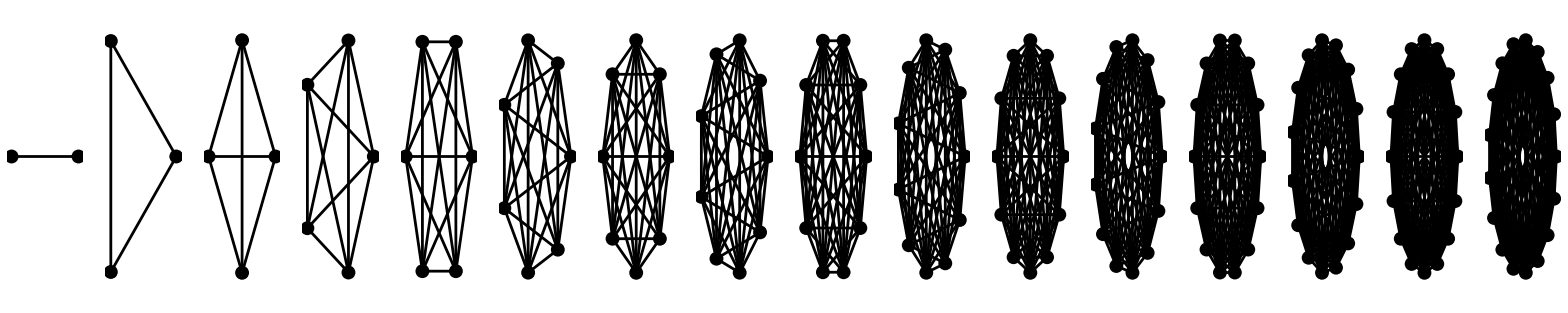

```mathematica
ShowGraphArray[Table[CompleteGraph[i],{i,2,17}]]
```

## 3. SUBGRAFOS Y GRAFOS BIPARTITOS

### 3.1. Subgrafos

### 3.2. Subgrafos inducidos

#### Función 6.9. IND[]

```mathematica
IND[W1_,F_]:=Module[{i},
F1={};
Do[If[Sort[Intersection[{F[[i]][[1]],F[[i]][[2]]},W1]]==Sort[{F[[i]][[1]],F[[i]][[2]]}],AppendTo[F1,F[[i]]]],{i,Length[F]}];
F1
]
```

#### Función 6.10. IND2[]

```mathematica
IND2[W1_,matrizadyacencia_]:=Module[{n,i,j},
n=Length[W1];
matrizadyacencia2=Table[0,{i,n},{j,n}];
Do[Do[
matrizadyacencia2[[i,j]]=matrizadyacencia[[W1[[i]],W1[[j]]]];
,{i,n}];
,{j,n}];
matrizadyacencia2
];
```

#### Ejemplo 6.7.

a)

```mathematica
IND[W1_,F_]:=Module[{i},
F1={};
Do[If[Sort[Intersection[{F[[i]][[1]],F[[i]][[2]]},W1]]==Sort[{F[[i]][[1]],F[[i]][[2]]}],AppendTo[F1,F[[i]]]],{i,Length[F]}];
F1
]
```

```mathematica
n=5;
W=Table[i,{i,n}];
F={};
Do[Do[AppendTo[F,i->j],{j,i+1,n}];,{i,n-1}];
IND[{2,3,4},F]
```

{2→3,2→4,3→4}

```mathematica
IND2[W1_,matrizadyacencia_]:=Module[{n,i,j},
n=Length[W1];
matrizadyacencia2=Table[0,{i,n},{j,n}];
Do[Do[
matrizadyacencia2[[i,j]]=matrizadyacencia[[W1[[i]],W1[[j]]]];
,{i,n}];
,{j,n}];
matrizadyacencia2
];
```

```mathematica
IND2[{2,3,4}, Table[If[i==j,0,1],{i,n},{j,n}]]
```

{{0,1,1},{1,0,1},{1,1,0}}

```mathematica
<<Combinatorica`
```

```mathematica
InduceSubgraph[CompleteGraph[5],{2,3,4}]
```

⁃Graph:<3,3,Undirected>⁃

b)

```mathematica
matrizadyacencia={{0,1,1,1,0},{0,0,1,0,0},{0,0,0,0,0},{0,0,1,0,0},{0,1,1,1,0}};
```

```mathematica
IND2[{2,3,4},matrizadyacencia]
```

{{0,1,0},{0,0,0},{0,1,0}}

```mathematica
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}];
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,Dimensions[matrizadyacencia][[1]]}];,{j,Dimensions[matrizadyacencia][[1]]}];
F
```

{1→2,5→2,1→3,2→3,4→3,5→3,1→4,5→4}

```mathematica
IND[{2,3,4},F]
```

{2→3,4→3}

### 3.3. Grafos bipartitos y bipartitos completos

#### Función 6.11. BIPARTITO[]

```mathematica
<<"Combinatorica`";
```

```mathematica
BIPARTITO[W_,F_]:=Module[{i,subconjuntos,j,fin},
bipartito=False;
i=1;
fin=Quotient[Length[W],2];
While[!bipartito && i<=fin,
subconjuntos=KSubsets[W,i];
j=1;
While[!bipartito && j<=Length[subconjuntos],
If[IND[subconjuntos[[j]],F]=={},
If[IND[Complement[W,subconjuntos[[j]]],F]=={},
bipartito=True;
W1=subconjuntos[[j]];
W2=Complement[W,subconjuntos[[j]]];
];
];
j++;];
i++;];
If[bipartito,Print["Es bipartito: W1=",W1," y W2=",W2];
If[Length[F]==Length[W1]*Length[W2],Print["Es bipartito completo: ",Subscript["K", Length[W1],Length[W2]]  ], Print["No es bipartito completo"]];
,Print["No es bipartito"]];
]
```

#### Ejemplo 6.8.

```mathematica
n=6;
W=Table[i,{i,n}]
F={};
Do[Do[AppendTo[F,i->j],{j,i+1,n}];,{i,n-1}];
F
```

{1,2,3,4,5,6}

{1→2,1→3,1→4,1→5,1→6,2→3,2→4,2→5,2→6,3→4,3→5,3→6,4→5,4→6,5→6}

```mathematica
<<"Combinatorica`";
```

```mathematica
IND[W1_,F_]:=Module[{i},
F1={};
Do[If[Intersection[{F[[i]][[1]],F[[i]][[2]]},W1]=={F[[i]][[1]],F[[i]][[2]]},AppendTo[F1,F[[i]]]],{i,Length[F]}];
F1
]
```

```mathematica
BIPARTITO[W_,F_]:=Module[{i,subconjuntos,j,fin},
bipartito=False;
i=1;
fin=Quotient[Length[W],2];
While[!bipartito && i<=fin,
subconjuntos=KSubsets[W,i];
j=1;
While[!bipartito && j<=Length[subconjuntos],
If[IND[subconjuntos[[j]],F]=={},
If[IND[Complement[W,subconjuntos[[j]]],F]=={},
bipartito=True;
W1=subconjuntos[[j]];
W2=Complement[W,subconjuntos[[j]]];
];
];
j++;];
i++;];
If[bipartito,Print["Es bipartito: W1=",W1," y W2=",W2];
If[Length[F]==Length[W1]*Length[W2],Print["Es bipartito completo: ",Subscript["K", Length[W1],Length[W2]]  ], Print["No es bipartito completo"]];
,Print["No es bipartito"]];
]
```

```mathematica
BIPARTITO[W,F]
```

No es bipartito

```mathematica
BIPARTITO[{1,2,3,4,5,6},{1->4,1->5,1->6,2->4,2->5,2->6,3->4,3->5,3->6}]
```

Es bipartito: W1={1,2,3} y W2={4,5,6}

Es bipartito completo: K_(3,3)

#### Función 6.12. BC[]

```mathematica
BC[n_,m_]:=Module[{},
W=Table[i,{i,n+m}];
F={};
Do[Do[AppendTo[F,i->j],{i,n}];,{j,n+1,n+m}];
]
```

#### Ejemplo 6.9.

```mathematica
BC[n_,m_]:=Module[{},
W=Table[i,{i,n+m}];
F={};
Do[Do[AppendTo[F,i->j],{i,n}];,{j,n+1,n+m}];
]
```

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{},
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[F[[k,1]],F[[k,2]]]]=1;
matrizadyacencia[[F[[k,2]],F[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
```

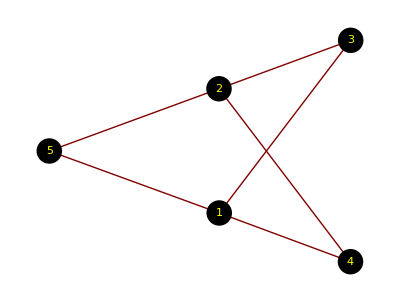

```mathematica
BC[2,3];
MA=MATRIZADYACENCIA[W,F];
GraphPlot[MA,VertexRenderingFunction->({Black,Disk[#,.07],Yellow,Text[#2,#1]}&)]
```

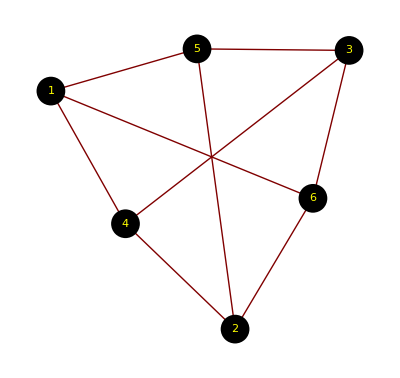

```mathematica
BC[3,3];
MA=MATRIZADYACENCIA[W,F];
GraphPlot[MA,VertexRenderingFunction->({Black,Disk[#,.07],Yellow,Text[#2,#1]}&)]
```

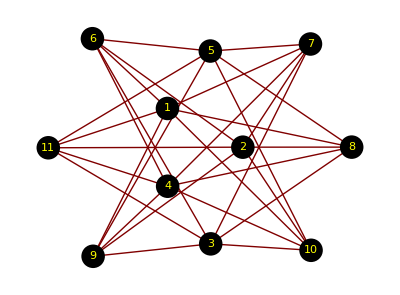

```mathematica
BC[5,6];
MA=MATRIZADYACENCIA[W,F];
GraphPlot[MA,VertexRenderingFunction->({Black,Disk[#,.07],Yellow,Text[#2,#1]}&)]
```

```mathematica
<<Combinatorica`
```

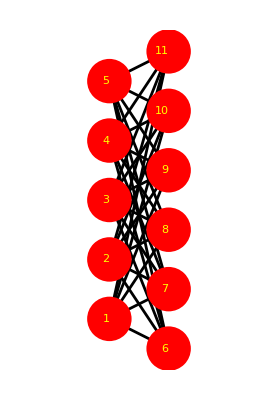

```mathematica
G=CompleteKPartiteGraph[5,6];
ShowGraph[G,VertexColor->Red, VertexStyle->PointSize[0.08],VertexNumber->True,VertexNumberColor->Yellow,VertexNumberPosition->{+.02,+.0}]
```

```mathematica
BipartiteQ[G]
```

True

#### Función 6.13. BCadyacencia[]

```mathematica
BCadyacencia[n_,m_]:=Table[If[(i≤n &&j≤n)||(i>n &&j>n),0,1],{i,n+m},{j,n+m}];
```

#### Ejemplo 6.10.

```mathematica
BCadyacencia[n_,m_]:=Table[If[(i≤n &&j≤n)||(i>n &&j>n),0,1],{i,n+m},{j,n+m}];
```

```mathematica
MatrixForm[BCadyacencia[5,5]]
```

(0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0)

#### Ejemplo 6.11.

```mathematica
BCadyacencia[n_,m_]:=Table[If[(i≤n &&j≤n)||(i>n &&j>n),0,1],{i,n+m},{j,n+m}];
```

```mathematica
<<"GraphUtilities`";
```

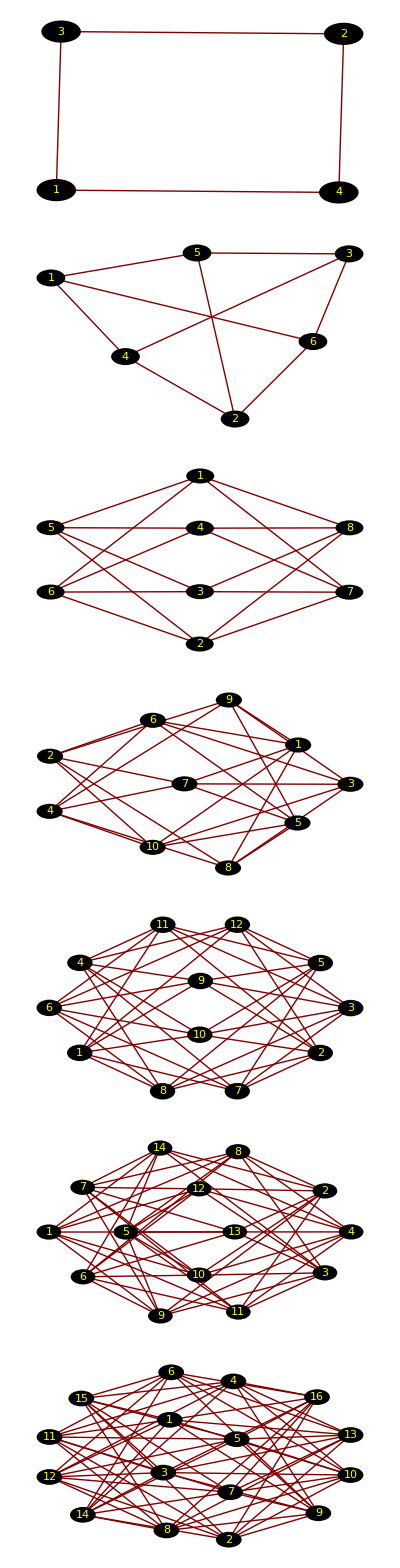

```mathematica
listado={};
Do[A=BCadyacencia[i,i];
AppendTo[listado,GraphPlot[A,VertexRenderingFunction->({Black,Disk[#,.07],Yellow,Text[#2,#1]}&)]];
,{i,2,8}];
TableForm[listado]
```

### 3.4. Complemento de un grafo

#### Ejemplo 6.12.

```mathematica
W={1,2,3,4,5,6};
F1={1->4,1->5,1->6,2->4,2->5,2->6,3->4,3->5,3->6};
```

```mathematica
n=6;
F={};
Do[Do[AppendTo[F,i->j],{j,i+1,n}];,{i,n-1}];
```

```mathematica
Wc=W
Fc=Complement[F,F1]
```

{1,2,3,4,5,6}

{1→2,1→3,2→3,4→5,4→6,5→6}

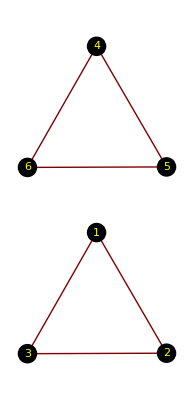

```mathematica
GraphPlot[Fc,VertexRenderingFunction->({Black,Disk[#,.07],Yellow,Text[#2,#1]}&)]
```

```mathematica
<<Combinatorica`
```

```mathematica
G=FromOrderedPairs[Table[{F1[[i]][[1]],F1[[i]][[2]]},{i,Length[F1]}],Type->Undirected];
```

⁃Graph:<9,6,Undirected>⁃

```mathematica
GraphComplement[G]
```

⁃Graph:<6,6,Undirected>⁃